```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
On[Assert]
```

```mathematica
(* INITIALISE HYPERPARAMETERS AND OBTAIN LOWEST LYING STATE *)
(**** !!!TUNABLE PARAMETERS!!! ****)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=1;(* Isospin *)
γMax=10;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=bq;(* mass of quark 1 *)
m2=bq;(* mass of quark 2 *)
m3=uq;(* mass of quark 3 *)
rangeMin=0.3;(* Minimum of ω range rangeMin≤ω≤rangeMax *)
rangeMax=0.75; (* max of ω range*)
increment=0.01;(* step size (increment size) *)
save=False;(* Do you want to save the {Subscript[ω, i],Subscript[E, i]} for rangeMin≤ω≤rangeMax data to: 'lines/Silvestre/eigenValues/Subscript[q, 1] Subscript[q, 2] Subscript[q, 3]/E{γMax}.mx'? *)
(* Example path: 'lines/Silvestre/eigenValues/uub/E8.mx' *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(* Save path parameters *)
If[save,
dirPath=FileNameJoin[{NotebookDirectory[],"lines/Silvestre/eigenValues"}];
quarkDict=Association[{uq->"u",sq->"s",cq->"c",bq->"b"}];
filename=quarkDict[m1]<>quarkDict[m2]<>quarkDict[m3]<>"/"<>"E"<>ToString[γMax]<>".mx"
]

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
t1=tMatrix[J,P,Λ,γMax,m1,m2,m3,1];
t2=tMatrix[J,P,Λ,γMax,m1,m2,m3,2];

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
```

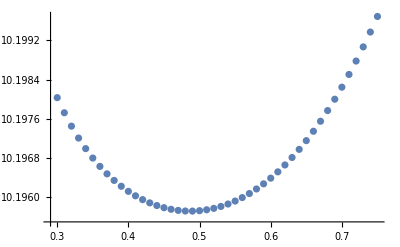

{14.3408,14.3321,14.2744,14.2332,14.2133,14.2085,14.1215,14.1099,14.1043,14.0626,14.0169,14.012,13.9731,13.9438,13.871,13.7613,13.7367,13.7024,13.6621,13.608,13.5603,13.0719,13.0389,13.0282,12.932,12.8937,12.8891,12.8613,12.7725,12.7488,12.7259,12.7142,12.6734,12.6523,12.6186,12.5713,12.1422,12.1042,12.101,12.0288,11.9697,11.9663,11.9542,11.846,11.8199,11.653,11.4837,11.4682,11.4362,11.2914,11.2556,11.0054,10.8967,10.8758,10.5549,10.1957,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Successfully Found Minimum

{0.49,10.1957}

```mathematica
(* Obtain a table of {{ω,E}} sets for varying ω to determine lowest Eigenvalue *)
tab=Table[{ω,Eigenvalues[Hb[J,P,Isospin,Λ,γMax,ω,m1,m2,m3,project]][[-firstNonZero]]},{ω,rangeMin,rangeMax,increment}];

(* Plot the list of above set of {{ω,E}} (The U-plot) *)
ListPlot[tab]

(* Extract ω's and Eigenvalues separately *)
omegas=tab[[All,1]];
evals=tab[[All,2]];
(* Find value of minimum eigenvalue *)
minEval=Min[evals];
(* Find positional index of minimum eigenvalue *)
posOfMinEval=Position[evals,minEval][[1,1]];
(* Use positional index of minimum eigenvalue to obtain the corresponding value of ω *)
optimumOmega=omegas[[posOfMinEval]];
(* Construct a list object containing {Subscript[ω, min],Subscript[E, min]} *)
minimum={optimumOmega,minEval};
(* Obtain wMin *)
wMin=minimum[[1]];

(* Print all eigenvalues for all ω's *)
Print[Eigenvalues[Hb[J,P,Isospin,Λ,γMax,optimumOmega,m1,m2,m3,project]]//Chop]

(* Initiate an error counter, will go up by one for each error encountered *)
errors=0;
(* First, check if the list object {Subscript[ω, min],Subscript[E, min]} exists in the list of all {{ω,E}} *)
If[tab[[posOfMinEval]]!=minimum,errors+=1;Print["Does not agree"]]
(* Check if Subscript[E, min] is the first element of {{ω,E}}, if True, extend ω range to the left *)
If[posOfMinEval==1,errors+=1;Print["Need to extend range more to the left"]]
(* Check if Subscript[E, min] is the last element of {{ω,E}}, if True, extend ω range to the right *)
If[posOfMinEval==Length[tab],errors+=1;Print["Need to extend range more to the right"]]
(* Finally if no errors encountered print {Subscript[ω, min],Subscript[E, min]} *)
If[errors==0,Print["Successfully Found Minimum"];Print[minimum];]

(* Save data *)
If[save==True,
fullPath=FileNameJoin[{dirPath,filename}];
Print["Successfully saved to:"];
Export[fullPath,tab]]
```

{0.4,0.5,0.6,0.7,0.8}

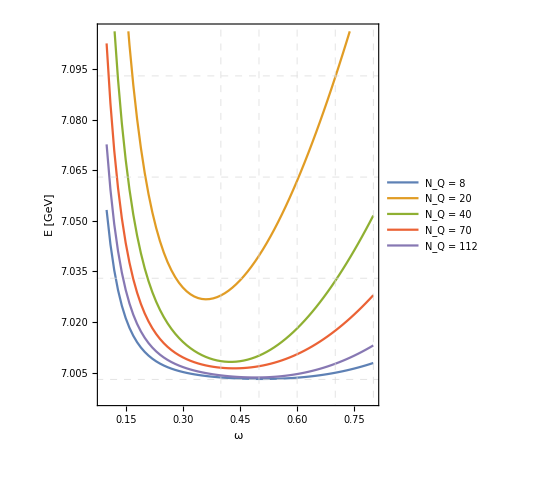

```mathematica
(* PLOTTING MASS PLOTS *)
allLinePaths=FileNames[All,"lines/Silvestre/eigenValues/scb"];
allFilenames=Table[FileNameJoin[{NotebookDirectory[],allLinePaths[[i]]}],{i,1,Length[allLinePaths]}];
allLinesData=Table[Import[allFilenames[[i]]],{i,1,Length[allFilenames]}];

plotRange={{0.09,0.8},Automatic};
frameTicks={{Automatic,None}, {Automatic,None}};
legendFontSize=14;
labelFontSize=14;
fontFamily="Times";
plotLegends={Placed[{Style["N_Q = 8",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 20",FontSize->legendFontSize,FontFamily->fontFamily],Style["N_Q = 40",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 70",FontSize->legendFontSize,FontFamily->fontFamily],
Style["N_Q = 112",FontSize->legendFontSize,FontFamily->fontFamily]
},{Center,Top}]};
labelStyle={FontSize->labelFontSize, FontFamily->fontFamily,Black};
frameLabel={{"E [GeV]",None},{"ω","Ω_cb, (scb)"}};
frame={{True,True},{True,True}};
vertGridLines=Table[7.003+x,{x,0,0.1,0.03}];
horzGridLines=Table[x,{x,0.4,0.8,0.1}]
gridLines={horzGridLines,vertGridLines};
gridLinesStyle=Directive[Dashed, LightGray];

plot=ListPlot[allLinesData,Joined->True,PlotRange->plotRange,
FrameTicks->frameTicks,
PlotLegends->plotLegends,
LabelStyle->labelStyle,
FrameLabel->frameLabel,
Frame->frame,
AspectRatio->1.2,
GridLines->gridLines,
GridLinesStyle->gridLinesStyle]
```

```mathematica
(* TODO: bb states plot up to 112, try 168 (γ=12),
TODO: understand what Silvestre means by quanta *)
```

```mathematica
Export["plots/baryons/eigVals/scbEvsW.pdf",plot,"PDF","AllowRasterization"->False]
```

plots/baryons/eigVals/scbEvsW.pdf